## Fast Slow System

### Plot0

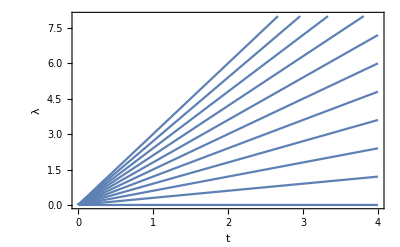

```mathematica
Plot[Table[r t,{r,0,3,.3}],{t,0,4},PlotRange->{{0,4},{0,8}},Frame->True,FrameLabel->{"t","λ"},LabelStyle->Directive[16]]
```

### Plot0a

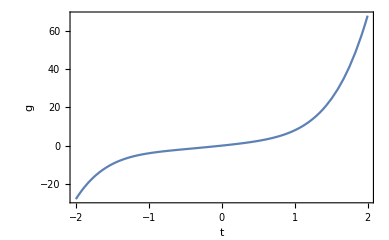

```mathematica
Plot[4t+t^2 + t^3+t^4+t^5,{t,-2,2},Frame->True,FrameLabel->{"t","g"},LabelStyle->Directive[16]]
```

### Plot1

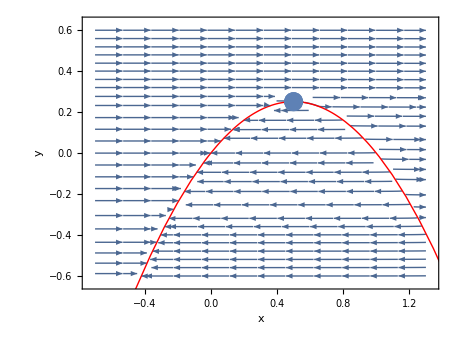

```mathematica
ϵ = .0001;
λ = 0;
p0= ListPlot[{{0,0}},PlotStyle->PointSize[Large]];
p1=StreamPlot[{(y + λ + x(x-1))/ϵ,-Sum[x^n,{n,1,5}]},{x,-.7,1.3},{y,-.6,.6},StreamPoints->Fine];
p2=Plot[-λ-x(x-1),{x,-2,2},PlotStyle->{Thick,Red},PlotRange->{-2,2}];
p3 = ParametricPlot[{0,y},{y,-.6,.6},PlotStyle->{Thick, Orange}];
p00= ListPlot[{{0.5,0.25}},PlotStyle->PointSize[.03]];
Show[p1,p2,p00,FrameLabel->{x,y}, AspectRatio->.75,LabelStyle->{16,GrayLevel[0]}]
```

### Plot2

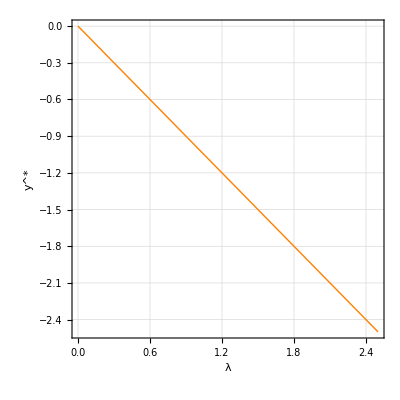

```mathematica
ParametricPlot[{λ,-λ},{λ,0,2.5},Frame->True,PlotStyle->Directive[Orange,Thick],FrameLabel->{"λ",Superscript["y","*"]},LabelStyle->{18,GrayLevel[0]},GridLines->Automatic]
```

### Plot3

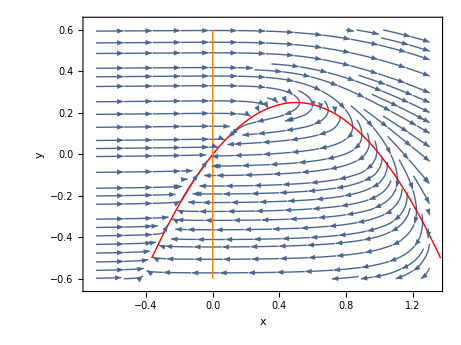

```mathematica
ϵ = .0001;
λ = 0;
p2=Plot[-λ-x(x-1),{x,-2,2},PlotStyle->{Thick,Red},PlotRange->{{-.7,1.3},{-.5,.5}}];
p3 = ParametricPlot[{0,y},{y,-.6,.6},PlotStyle->{Thick, Orange}];
p4=Graphics[Arrow[{{-.1,.3},{.15,.3}}]];
p5=Graphics[Arrow[{{.1,-.4},{-.15,-.4}}]];
p6=Graphics[Arrow[{{-.2,-.3},{-.2,-.1}}]];
p7=Graphics[Arrow[{{.9,.15},{.9,-.05}}]];
Show[p1,p2, p3,FrameLabel->{x,y},Frame->True,Axes->False,AspectRatio->.75,LabelStyle->{16,GrayLevel[0]}]
```

### Plot4

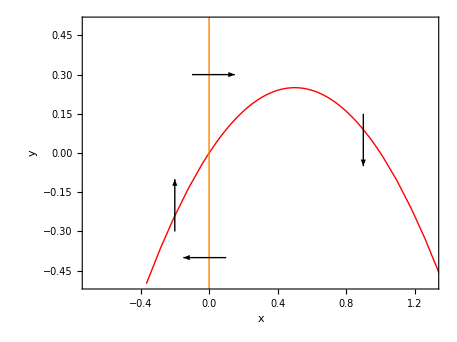

```mathematica
ϵ = .02;
λ = 0;
p2=Plot[-λ-x(x-1),{x,-2,2},PlotStyle->{Thick,Red},PlotRange->{{-.7,1.3},{-.5,.5}}];
p3 = ParametricPlot[{0,y},{y,-.6,.6},PlotStyle->{Thick, Orange}];
p4=Graphics[Arrow[{{-.1,.3},{.15,.3}}]];
p5=Graphics[Arrow[{{.1,-.4},{-.15,-.4}}]];
p6=Graphics[Arrow[{{-.2,-.3},{-.2,-.1}}]];
p7=Graphics[Arrow[{{.9,.15},{.9,-.05}}]];
Show[p2, p3,p4,p5,p6,p7,FrameLabel->{x,y},Frame->True,Axes->False,AspectRatio->.75,LabelStyle->{16,GrayLevel[0]}]
```

### Plot4a

```mathematica
Clear[x,y]
```

```mathematica
ϵ = .02;
λ = 0;
p2=Plot[-λ-x(x-1),{x,-2,2},PlotStyle->{Thick,Red},PlotRange->{{-.7,1.3},{-.5,.5}}];
p33[rr_]:= ParametricPlot[{rr,y},{y,-.6,.6},PlotStyle->{Thick, Orange}];
p44[rr_]:=Graphics[Arrow[{{-.1+rr,.3},{.15+rr,.3}}]];
p55[rr_]:=Graphics[Arrow[{{.1+rr,-.4},{-.15+rr,-.4}}]];
p66=Graphics[Arrow[{{-.2,-.3},{-.2,-.1}}]];
p77=Graphics[Arrow[{{.9,.15},{.9,-.05}}]];
zzz=Table[Show[p2,p33[r],p44[r],p55[r],p66,p77,FrameLabel->{x,y},Frame->True,Axes->False,AspectRatio->.75,LabelStyle->{16,GrayLevel[0]}],{r,0,.8,.1}];
```

```mathematica
Export["~/Desktop/animation1.gif",zzz]
```

~/Desktop/animation1.gif

-Graphics-

### Plot5

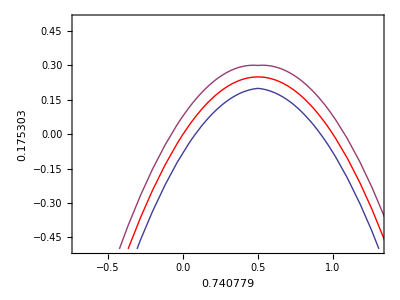

```mathematica
ϵ = .01;
λ = 0;
p25=Plot[{-λ-x(x-1)-.05- .03Abs[2x-1],-λ-x(x-1)+.05 + .03Abs[2x-1]},{x,-2,2},PlotRange->{{-.7,1.3},{-.5,.5}}];
Show[p2,p25,FrameLabel->{x,y},Frame->True,Axes->False,AspectRatio->.75]
```

### Plot6

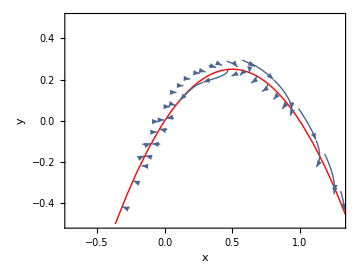

```mathematica
ϵ = .01;
λ = 0;
p2=Plot[-λ-x(x-1),{x,-2,2},PlotStyle->{Thick,Red},PlotRange->{{-.7,1.3},{-.5,.5}}];
p23=StreamPlot[If[y>-λ-x(x-1)-.05- .03Abs[2x-1] &&y<-λ-x(x-1)+.05+ .03Abs[2x-1] ,{(y + λ + x(x-1))/ϵ,-Sum[x^n,{n,1,5}]},{,}],{x,-1,1.4},{y,-.5,.5},PlotRange->{{-.7,1.3},{-.5,.5}},StreamPoints->Fine,ImageSize->Medium]
Show[p2,p23,FrameLabel->{x,y},Frame->True,Axes->False,AspectRatio->.75]
```

### Plot7

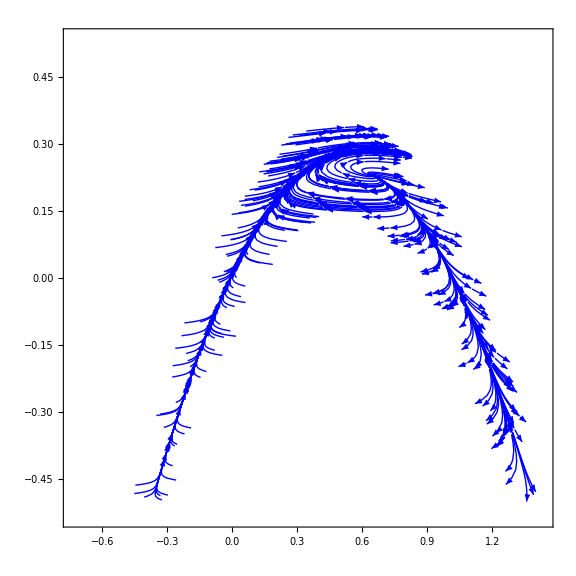

```mathematica
ϵ=.005;
g=StreamPlot[If[y>-λ-x(x-1)-.1- .05Abs[2x-1] &&y<-λ-x(x-1)+.1+ .05Abs[2x-1] ,{(y + λ + x(x-1))/ϵ,1.6-Sum[x^n,{n,1,5}]},{,}],{x,-.7,1.4},{y,-.5,.5},StreamStyle->Blue,StreamPoints->{Table[{RandomReal[{-.7,1.4}],RandomReal[{-.5,.5}]},{i,0,1000}],Automatic,10},ImageSize->Large];
Show[g]
```

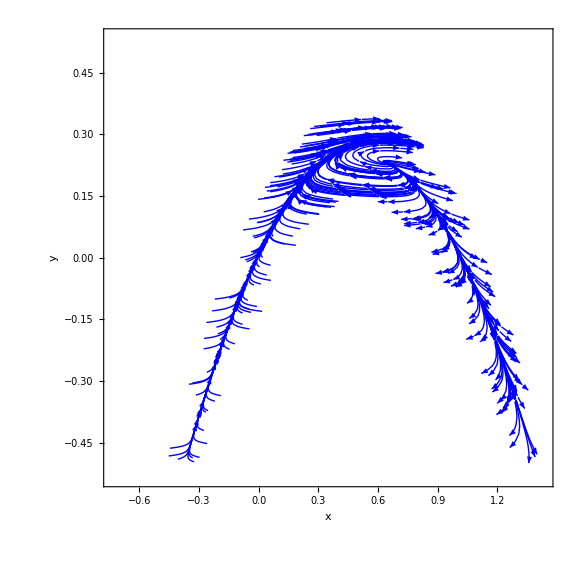

```mathematica
Show[%75,FrameLabel->{{HoldForm[y],None},{HoldForm[x],None}},PlotLabel->None,LabelStyle->{FontFamily->"Al Bayan",16,GrayLevel[0]}]
```

### Plot8

```mathematica
CoolColor[ z_ ] :=RGBColor[z,1-z,1];
```

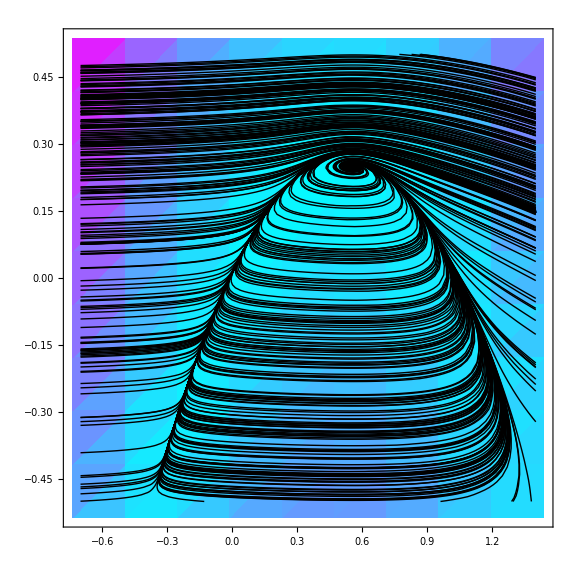

```mathematica
ϵ=.01;
g=StreamDensityPlot[{(y + λ + x(x-1))/ϵ,1.2-Sum[x^n,{n,1,5}]},{x,-.7,1.4},{y,-.5,.5},StreamPoints->{Table[{RandomReal[{-.7,1.4}],RandomReal[{-.5,.5}]},{i,0,400}],Automatic,10},ImageSize->Large,StreamStyle->"Line",ColorFunction->CoolColor];
Show[g]
```

```mathematica
?ColorFunction
```

ColorFunction is an option for graphics functions that specifies a function to apply to determine colors of elements.

```mathematica
M = {{-1/e,1/e},{-gg,0}}
```

{{-1/e,1/e},{-gg,0}}

```mathematica
Eigenvalues[M]
```

{(-1-√(1-4 e gg))/(2 e),(-1+√(1-4 e gg))/(2 e)}

### Plot10

```mathematica
Plot[{(Sqrt[r]+r^.8).3,.5},{r,0,2},Frame->True,FrameLabel->{r,x},PlotStyle->{Thick,Dashed},LabelStyle->Directive[16]]
```

```mathematica
Superscript["g",-1]
```

g^-1

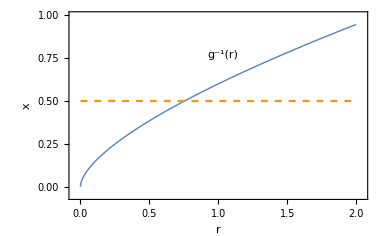

## Image of vector field with equilibrium

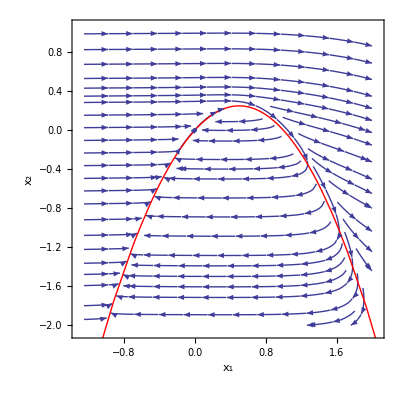

```mathematica
ϵ = .01;
λ = 0;
p0= ListPlot[{{0,0}},PlotStyle->PointSize[Large],ImagePadding->All];
p1=StreamPlot[{(y + λ + x(x-1))/ϵ,.5-Sum[x^n,{n,1,5}]},{x,-1.25,2},{y,-2,1},ImagePadding->All];
p2=Plot[-λ-x(x-1),{x,-5,5},PlotStyle->{Thick,Red},PlotRange->{-5,5},ImagePadding->All];
Show[p1,p2,p0, FrameLabel->{Subscript["x",1],Subscript["x",2]},LabelStyle->Directive[14]]
```

## Image of Critical manifold and QSE and fold

### Plot9

```mathematica
p3=ParametricPlot3D[{x,-λλ-x(x-1),λλ},{x,-1,2},{λλ,0,2.5},PlotRange->{{-1,2},{-4,.5},{0,2.5}},PlotStyle->Directive[Opacity[0.4],Blue],Mesh->None,AxesLabel->{"x","y","λ"}];
p4=ParametricPlot3D[{0,-λλ,λλ},{λλ,0,2.5},PlotRange->{{-1,3},{-4,.5},{0,2.5}},PlotStyle->{Red,Thickness[.02]}];
p5=ParametricPlot3D[{1/2,-λλ+1/4,λλ},{λλ,0,2.5},PlotRange->{{-1,2},{-4,.5},{0,2.5}},PlotStyle->{Green,Thickness[.02],Dashed}];Show[p3,p4,p5,LabelStyle->Directive[16]]
```

-Graphics3D-

## Image of several trajectories

```mathematica
Clear[x,y,L,t,ϵ]
r = .4;
ϵ = .02;
sol = NDSolve[{
x'[t]==(y[t] + L[t]+x[t](x[t]-1))/ϵ,
y'[t]==-Sum[x[t]^n,{n,1,5}],
L'[t]==r,
x[0]==0,y[0]==0,L[0]==0},{x,y,L},{t,0,20}];
p6 = ParametricPlot3D[{x[t],y[t],L[t]}/.sol,{t,0,20},PlotRange->{{-1,2},{-4,.5},{0,2.5}},PlotStyle->{Yellow,Thickness[.015]}];

Clear[x,y,L,t,ϵ]
r = .98;
ϵ = .02;
sol = NDSolve[{
x'[t]==(y[t] + L[t]+x[t](x[t]-1))/ϵ,
y'[t]==-Sum[x[t]^n,{n,1,5}],
L'[t]==r,
x[0]==0,y[0]==0,L[0]==0},{x,y,L},{t,0,20}];
p7 = ParametricPlot3D[{x[t],y[t],L[t]}/.sol,{t,0,20},PlotRange->{{-1,2},{-4,.5},{0,2.5}},PlotStyle->{Gray,Thickness[.015]}];

Clear[x,y,L,t,ϵ]
r = 1.07;
ϵ = .02;
sol = NDSolve[{
x'[t]==(y[t] + L[t]+x[t](x[t]-1))/ϵ,
y'[t]==-Sum[x[t]^n,{n,1,5}],
L'[t]==r,
x[0]==0,y[0]==0,L[0]==0},{x,y,L},{t,0,20}];
p8 = ParametricPlot3D[{x[t],y[t],L[t]}/.sol,{t,0,20},PlotRange->{{-1,2},{-4,.5},{0,2.5}},PlotStyle->{Blue,Thickness[.015]}];

Clear[x,y,L,t,ϵ]
r = 1.2;
ϵ = .02;
sol = NDSolve[{
x'[t]==(y[t] + L[t]+x[t](x[t]-1))/ϵ,
y'[t]==-Sum[x[t]^n,{n,1,5}],
L'[t]==r,
x[0]==0,y[0]==0,L[0]==0},{x,y,L},{t,0,1}];
p9 = ParametricPlot3D[{x[t],y[t],L[t]}/.sol,{t,0,1},PlotRange->{{-1,2},{-4,.5},{0,2.5}},PlotStyle->{Purple,Thickness[.015]}];
Show[p3,p4,p5,p6,p7,p8,p9, LabelStyle->Directive[16]]
```

-Graphics3D-

## Images with logistic forcing

```mathematica
Clear[x,y,L,t,ϵ]
r = .5;
ϵ = .02;
sol = NDSolve[{
x'[t]==(y[t] + L[t]+x[t](x[t]-1))/ϵ,
y'[t]==-Sum[x[t]^n,{n,1,5}],
L'[t]==r E^(-L[t]),
x[0]==0,y[0]==0,L[0]==0},{x,y,L},{t,0,20}];
pp1 = ParametricPlot3D[{y[t],x[t],L[t]}/.sol,{t,0,20},PlotRange->{{-2,.5},{-1,2},{0,2}},PlotStyle->{Green,Thick}];

Clear[x,y,L,t,ϵ]
r = 1.5;
ϵ = .02;
sol = NDSolve[{
x'[t]==(y[t] + L[t]+x[t](x[t]-1))/ϵ,
y'[t]==-Sum[x[t]^n,{n,1,5}],
L'[t]==r E^(-L[t]),
x[0]==0,y[0]==0,L[0]==0},{x,y,L},{t,0,20}];
pp2 = ParametricPlot3D[{y[t],x[t],L[t]}/.sol,{t,0,20},PlotRange->{{-2,.5},{-1,2},{0,2}},PlotStyle->{Blue,Thick}];

Clear[x,y,L,t,ϵ]
r = 2.5;
ϵ = .02;
sol = NDSolve[{
x'[t]==(y[t] + L[t]+x[t](x[t]-1))/ϵ,
y'[t]==-Sum[x[t]^n,{n,1,5}],
L'[t]==r E^(-L[t]),
x[0]==0,y[0]==0,L[0]==0},{x,y,L},{t,0,20}];
pp3 = ParametricPlot3D[{y[t],x[t],L[t]}/.sol,{t,0,20},PlotRange->{{-2,.5},{-1,2},{0,2}},PlotStyle->{Purple,Thick}];
```

```mathematica
Show[p3,p4,p5,pp1,pp2,pp3]
```

-Graphics3D-

## Periodic Forcing

```mathematica
Clear[x,y,L,t,ϵ,A]
A = .5;
w = 5;
ϵ = .02;
sol = NDSolve[{
x'[t]==(y[t] + L[t]+x[t](x[t]-1))/ϵ,
y'[t]==-Sum[x[t]^n,{n,1,5}],
L'[t]==-A 2Pi w Sin[2Pi t w],
x[0]==0,y[0]==0,L[0]==0},{x,y,L},{t,0,17}];
q1 = ParametricPlot3D[{y[t],x[t],L[t]}/.sol,{t,10,15},PlotRange->All,PlotStyle->{Purple,Thick}];
Show[p3,p4,p5,q1]
```

-Graphics3D-

## Co-Moving System

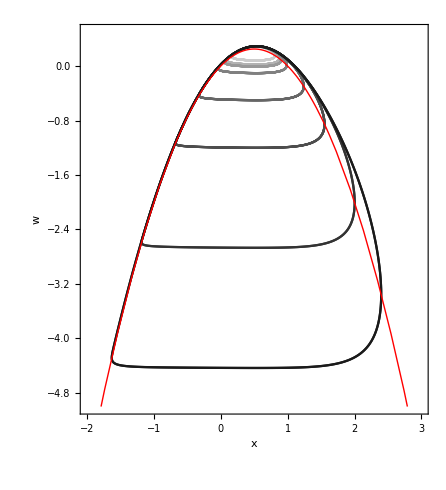

```mathematica
Clear[x,y,L,t,ϵ,w]
r = 1.05;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp01 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.8],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.065;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp02 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.7],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.07;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp03 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.6],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.08;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp04 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.5],Frame->True];
r = 1.09;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp05 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.4],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.0917;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp06 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.3],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.092;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp07 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.2],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.09205;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp08 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.1],Frame->True];
p10=Plot[-x(x-1),{x,-5,5},PlotStyle->{Thick,Red},PlotRange->{-5,5}];
Show[pp01,pp02, pp03,pp04,pp05,pp06,pp07,pp08,p10,FrameLabel->{x,w},PlotRange->{{-2,3},{-5,.5}},Axes->False,Frame->True,LabelStyle->Directive[16]]
```

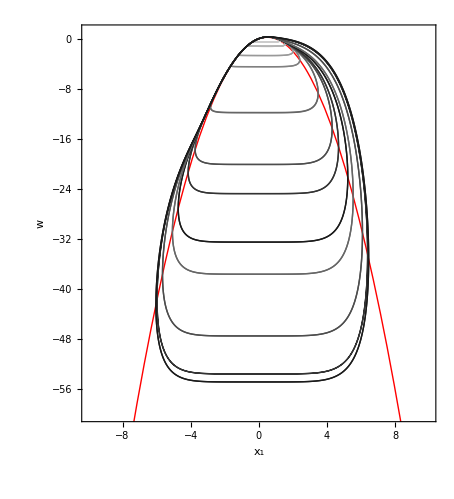

```mathematica
Clear[x,y,L,t,ϵ,w]
r = 1.09;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp01 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.8],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.0917;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp02 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.7],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.092;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp03 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.6],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.09205;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp04 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.5],Frame->True];
r = 1.0921;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp05 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.4],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.09215;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp06 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.3],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.0922;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp07 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.2],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.0924;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp08 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.1],Frame->True];
r = 1.0928;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp09 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.4],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.1;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp10 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.3],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.2;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp11 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.2],Frame->True];
Clear[x,y,L,t,ϵ]
r = 1.3;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1))/ϵ,
w'[t]==r-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp12 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.1],Frame->True];
p10=Plot[-x(x-1),{x,-10,10},PlotStyle->{Red},PlotRange->{-100,5}];
Show[p10,pp01,pp02, pp03,pp04,pp05,pp06,pp07,pp08,pp09,pp10,pp11,pp12,FrameLabel->{Subscript[x,1],w},PlotRange->{{-10,10},{-60,1}},AspectRatio->1.1,Axes->False,Frame->True,LabelStyle->Directive[16]]
```

```mathematica
Clear[x,y,L,t,ϵ,w]
r = 1.05;
ϵ = .02;
sol = NDSolve[{
x'[t]==(w[t]+x[t](x[t]-1.04))/ϵ -.1x[t]^3,
w'[t]==r+.4w[t]-Sum[x[t]^n,{n,1,5}],
x[0]==-2,w[0]==1},{x,w},{t,0,20}];
pp01 = ParametricPlot[{x[t],w[t]}/.sol,{t,15,20},PlotRange->{All,{-2,1}},PlotPoints->10000,PlotStyle->GrayLevel[.8],Frame->True];
```

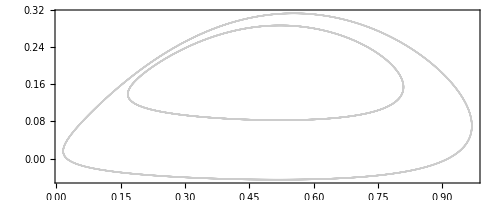

```mathematica
Show[pp01,pp02,PlotRange->All]
```

## 3 plots of tipping

### 1st plot

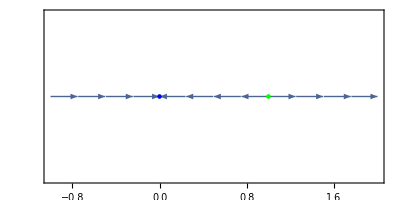

```mathematica
p2= ListPlot[{{0,0}},PlotStyle->{Directive[Blue,PointSize[Large]]}];
p3 =  ListPlot[{{1,0}},PlotStyle->{Directive[Green,PointSize[Large]]}];
pp07=StreamPlot[{x(x-1),0},{x,-1,2},{t,-.05,.05},AspectRatio->1/2];
Show[p2,p3,pp07,Frame->True,Axes->False,PlotRange->{{-1,2},{-.1,.1}},FrameTicks->{True,None},AspectRatio->1/2]
```

### 2nd plot

```mathematica
λ[t_]:=.1t;
```

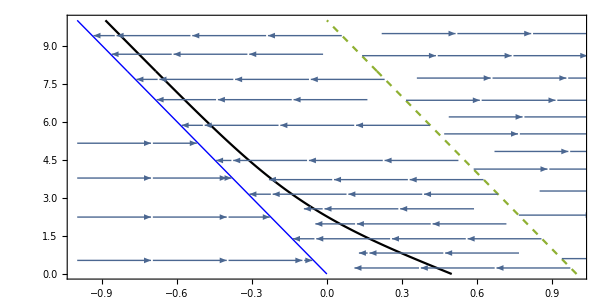

```mathematica
sol=NDSolve[{
x'[t]==(x[t]+λ[t])(x[t]-1+λ[t]),
x[0]==.5},{x},{t,0,20}];
pp01 = ParametricPlot[{{x[t],t}/.sol,{-λ[t],t},{-λ[t]+1,t}},{t,0,10},PlotStyle->{Black,Directive[Thick,Blue],Dashed},PlotRange->All,PlotPoints->10000,Frame->True,AspectRatio->1];
pp02 = StreamPlot[{(x+λ[t])(x-1+λ[t]),0},{x,-1,2},{t,0,10},StreamPoints->Coarse];
Show[pp01,pp02,PlotRange->{{-1,1},All},AspectRatio->1/2]
```

### 3rd plot

```mathematica
λ[t_]:=.3t;
```

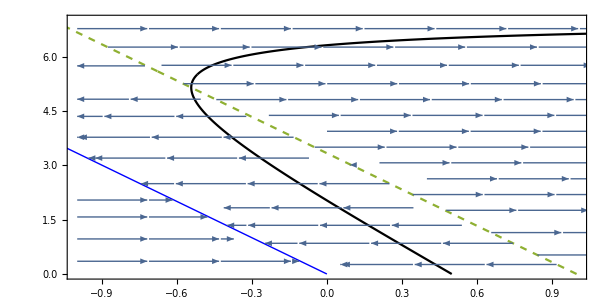

```mathematica
sol=NDSolve[{
x'[t]==(x[t]+λ[t])(x[t]-1+λ[t]),
x[0]==.5},{x},{t,0,20}];
pp01 = ParametricPlot[{{x[t],t}/.sol,{-λ[t],t},{-λ[t]+1,t}},{t,0,7},PlotStyle->{Black,Directive[Thick,Blue],Dashed},PlotRange->All,PlotPoints->10000,Frame->True,AspectRatio->1];
pp02 = StreamPlot[{(x+λ[t])(x-1+λ[t]),0},{x,-1,2},{t,0,7},StreamPoints->Coarse];
Show[pp01,pp02,PlotRange->{{-1,1},All},AspectRatio->1/2]
```